# Fancy Maps

## Color Palette

```mathematica
originalColorsValues={
{70,50,0,0},
{0,100,0,0},
{0,0,0,0},
{100,100,100,100},
{0,0,0,0}
};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues
```

{CMYKColor[Rational[7, 10], Rational[1, 2], 0, 0],CMYKColor[0, 1, 0, 0],CMYKColor[0, 0, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

## Map With IDs

```mathematica
countryName="Democratic Republic of Sao Tome and Principe";
path = "~/Desktop/STPMap/";
raw=Import[path<>"stp_all_sites_v3.csv"][[2;;All]];
{latLongs,sizesPop}={raw[[All,1;;2]],raw[[All,3]]};
{center,gridSize}={Mean/@(latlongs//Transpose),1};
sizes=N[Log[#]]&/@sizesPop;
```

```mathematica
sizes
```

{5.40268,2.48491,2.07944,2.77259,3.13549,4.15888,3.3322,3.4012,2.99573,2.99573,5.81413,4.96981,4.02535,5.07517,3.46574,4.40672,4.52179,2.99573,3.80666,5.62762,4.85203,4.31749,2.99573,2.99573,1.94591,4.63473,5.52545,3.91202,5.44674,1.09861,5.43808,6.03069,3.78419,0.,5.27811,4.02535,5.49306,5.01064,5.69036,2.3979,3.73767,5.02388,4.70953,2.3979,4.5326,4.39445,4.5326,3.82864,6.19032,6.15486,5.96358,6.92756,5.33754,5.64191,4.80402,1.79176,4.58497,4.17439,7.85825,4.46591,4.09434,2.99573,3.8712,4.38203,3.29584,6.42162,6.10479,2.99573,0.,2.99573,2.99573,4.51086,5.3799,4.20469,4.58497,4.11087,6.44889,2.99573,2.48491,4.68213,7.52941,2.99573,5.71043,5.97889,4.26268,2.30259,3.78419,4.06044,2.3979,2.99573,5.1299,8.18563,5.50939,7.42118,5.69373,7.85825,5.826,6.57228,6.05209,7.36897,4.36945,3.2581,6.43455,4.02535,4.40672,4.06044,6.37673,5.4848,4.46591,4.75359,5.64897,5.31321,5.0626,5.30827,4.17439,5.67675,5.56068,5.45532,3.80666,6.67834,5.90536,6.39693,5.15906,6.47543,5.33272,6.21261,6.65286,7.24993,5.03044,2.77259,3.78419,4.18965,4.78749,1.09861,3.3673,5.26786,3.3322,5.23644,4.85981,2.99573,2.99573,1.38629,0.,3.8712,4.35671,4.54329,4.00733,2.99573,5.2832,2.19722,2.94444,1.60944,1.09861,6.52796,4.82831,5.65599,3.66356,2.99573,0.,2.63906,2.99573,2.3979,2.77259,4.07754,3.82864,2.94444,5.33272,5.12396,6.13773,4.77068,4.5326,2.89037,4.68213,4.68213,1.09861,4.59512,1.09861,3.78419,5.39816,2.30259,1.79176,3.17805,4.14313,5.23111,4.06044,1.09861,4.52179,1.79176,2.19722,5.25227,6.51915,4.7185,6.37161,4.64439,5.46806,2.70805,2.99573,5.11199,1.60944,3.85015,2.63906,3.43399,0.693147,5.95064,4.56435,2.99573,4.96981,2.99573,2.3979,3.55535,2.99573,6.77422,4.52179,5.5835,5.37064,6.91374,6.65801,5.63479,6.17794,6.2106,5.743,7.13569,4.84419,4.78749,5.61677,2.63906,4.30407,4.91998,7.03527,4.41884,5.03044,4.80402,5.81711,6.72263,6.56808,5.54908,4.65396,5.46383,5.77455,4.96981,4.82831,5.92158,6.49375,4.36945,6.02587,6.92854,6.48616,7.44775,4.44265,2.99573,5.19296,6.24804,5.79606,5.12396,4.12713,3.3322,5.8944,7.28482,6.12249,4.7362,5.56834,7.13489,7.88908,5.65249,2.99573,2.07944,3.71357,1.79176,4.14313,1.60944,4.64439,2.07944,4.06044,2.19722,6.06611,6.14847,5.21494,5.23111,5.3845,4.67283,2.30259,3.3322,0.,2.63906,1.94591,2.99573,4.7185,6.02102,6.49677,5.35659,6.64509,5.8944,6.32077,6.14419,7.55538,5.2575,6.30445,6.63988,6.90875,5.03695,4.02535,3.3322,3.21888,5.68358,5.12396,5.82008,4.43082,7.13489,5.826,5.00395,5.44242,5.19296,5.68017,5.63479,4.85203,5.09987,3.17805,6.77079,2.99573,2.99573,5.24702,0.,2.30259,1.94591,6.65415,6.37161,5.62762,5.80513,4.85203,3.17805,5.7301,4.51086,4.26268,2.99573,6.06611,2.99573,6.59851,5.24702,6.63068,1.79176,4.27667,4.17439,6.00881,4.98361,2.07944,5.15906,5.20401,5.44242,4.07754,2.83321,6.22456,2.48491,0.693147,1.60944,2.99573,7.02376,6.19441,6.40026,5.84932,5.55683,6.3699,4.74493,2.99573,6.89972,4.57471,3.68888,5.65599,5.82008,2.99573,2.99573,7.24708,6.12249,4.33073,3.21888,4.17439,5.48064,5.57973,1.79176,4.02535,4.21951,3.43399,3.85015,4.55388,6.95081,4.44265,5.49306,4.8828,2.30259,5.0814,5.91889,2.89037,5.98896,6.24804,6.4599,6.32794,4.85203,6.60394,5.66296,2.19722,5.34233,4.23411,6.96885,0.693147,1.94591,5.7869,6.07074,3.55535,5.3033,5.11199,3.63759,5.45532,6.22059,2.99573,2.99573,3.95124,3.13549,0.,1.38629,2.99573,3.97029,0.693147,0.693147,2.83321,1.94591,0.,2.99573,6.00635,5.7301,6.23441,5.35659,6.40688,5.33272,6.30992,6.67834,3.7612,2.99573,5.29832,2.99573,2.56495,2.99573,2.99573,4.33073,2.99573,2.99573,6.38012,6.93828,6.35437,5.87774,6.09582,6.62539,5.84932,7.37212,5.98394,6.37161,7.51534,6.2634,7.62462,5.7589,7.53956,6.44413,6.36819,8.44247,6.68711,7.5807,7.31322,7.9047,6.88141,8.1409,7.49165,6.89163,6.36475,7.81157,8.15047,6.56526,6.23832,6.286,6.38182,6.07074,6.44889,8.36614,7.71334,6.98286,8.19174,7.96067,5.88888,7.22402,5.45959,7.82963,5.79606,6.34388,5.8861,6.50129,5.97126,7.40974,7.0193,7.11558,6.2691,5.94017,4.65396,7.82963,6.09807,3.3322,2.48491,2.99573,2.99573,2.99573,4.30407,2.99573,2.19722}

GeoGraphics::color: Directive[{CMYKColor[0, 0, 0, 0],Opacity[1]}] is not a valid color or gray-level specification.

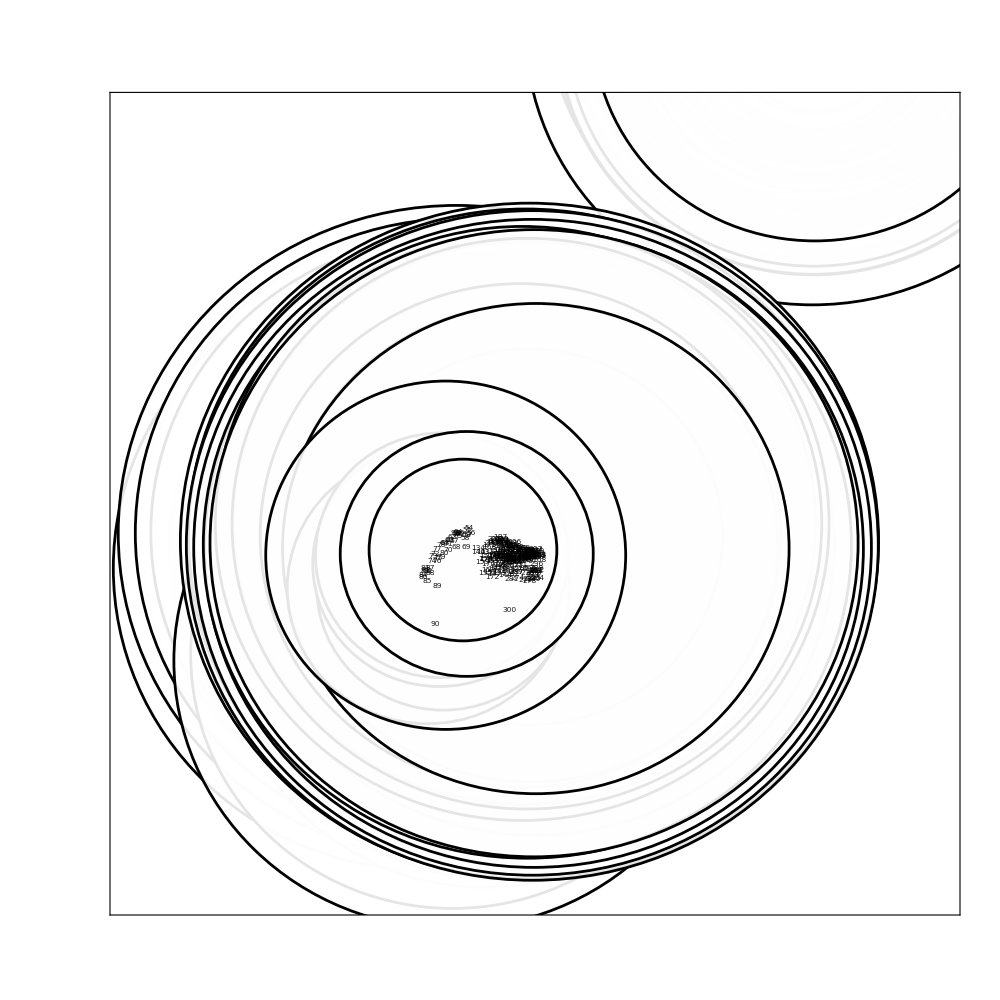

```mathematica
GeoGraphics[{
(*Quiet[GeoPosition/@CityData[{All,countryName}]],*)
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.030],Darker[colorPalette[[5]],.06]]],Opacity[.9],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.0075],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->1
,Axes->False
,Background->Directive[{colorPalette[[5]],Opacity[1]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]
,ImageSize->1000
,PlotRange->({#-gridSize,#+gridSize}&/@center)
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.002],Opacity[1],Black]],
Disk[#[[1]],0.01+#[[2]]/10]&/@Transpose[{latLongs,sizes//N}],
Text[Style[#[[2]],7.5,Black],#[[1]]]&/@Transpose[{latLongs,ToString/@Range[latLongs//Length]}],
Black,
Opacity[1],
Text[
Style[countryName,50,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.55gridSize,center[[2]]-gridSize*.8}]
}
]
(*Export["./images/"<>countryName<>"ID.png",%,ImageSize->2500,ImageResolution->500]*)
```

## Fonts

```mathematica
$FontFamilies;
Style[#,25,FontFamily->#]&/@%
```

{Al Bayan,Alegreya SC,Al Nile,Al Tarikh,American Typewriter,Andale Mono,Apple Braille,Apple Chancery,Apple Color Emoji,AppleGothic,AppleMyungjo,Apple SD Gothic Neo,Apple Symbols,Arial,Arial Black,Arial Hebrew,Arial Hebrew Scholar,Arial Narrow,Arial Rounded MT Bold,Arial Unicode MS,Athelas,Avenir,Avenir Next,Avenir Next Condensed,Ayuthaya,Baghdad,Bangla MN,Bangla Sangam MN,Baskerville,Beirut,Big Caslon,Bitstream Vera Sans Mono,Bodoni 72,Bodoni 72 Oldstyle,Bodoni 72 Smallcaps,Bodoni Ornaments,Bradley Hand,Brush Script MT,Chalkboard,Chalkboard SE,Chalkduster,Charter,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Cochin,Comic Sans MS,Copperplate,Corsiva Hebrew,Courier,Courier New,Cousine,Damascus,DecoType Naskh,Devanagari MT,Devanagari Sangam MN,Didot,DIN Alternate,DIN Condensed,Diwan Kufi,Diwan Thuluth,Droid Serif,EB Garamond,EB Garamond 12 All SC,EB Garamond SC,Economica,Euphemia UCAS,Farah,Farisi,Felipa,Futura,GB18030 Bitmap,Geeza Pro,Geneva,Gentium Basic,Georgia,Gill Sans,Gujarati MT,Gujarati Sangam MN,Gurmukhi MN,Gurmukhi MT,Gurmukhi Sangam MN,Heiti SC,Heiti TC,Helvetica,Helvetica Neue,Herculanum,Hiragino Kaku Gothic Pro,Hiragino Kaku Gothic ProN,Hiragino Kaku Gothic Std,Hiragino Kaku Gothic StdN,Hiragino Maru Gothic Pro,Hiragino Maru Gothic ProN,Hiragino Mincho Pro,Hiragino Mincho ProN,Hiragino Sans,Hiragino Sans GB,Hoefler Text,Impact,InaiMathi,Inconsolata,Iowan Old Style,ITF Devanagari,ITF Devanagari Marathi,Kailasa,Kalam,Kannada MN,Kannada Sangam MN,Kefa,Khmer MN,Khmer Sangam MN,Kohinoor Bangla,Kohinoor Devanagari,Kohinoor Telugu,Kokonor,Krungthep,KufiStandardGK,Lao MN,Lao Sangam MN,Lato,League Gothic,Lucida Grande,Luminari,Malayalam MN,Malayalam Sangam MN,Marion,Marker Felt,Menlo,Microsoft Sans Serif,Mishafi,Mishafi Gold,Monaco,Mshtakan,Muna,Myanmar MN,Myanmar Sangam MN,Nadeem,New Peninim MT,Noteworthy,Optima,Oriya MN,Oriya Sangam MN,Oswald,Palatino,Papyrus,Phosphate,PingFang HK,PingFang SC,PingFang TC,Plantagenet Cherokee,Playfair Display,PT Mono,PT Sans,PT Sans Caption,PT Sans Narrow,PT Serif,PT Serif Caption,Raanana,Roboto,Roboto Condensed,Roboto Slab,Sana,Sathu,Savoye LET,Seravek,Shadows Into Light Two,Shree Devanagari 714,SignPainter,Silom,Sinhala MN,Sinhala Sangam MN,Skia,Snell Roundhand,Songti SC,Songti TC,Source Code Pro,Source Sans Pro,Source Serif Pro,STIXGeneral,STIXIntegralsD,STIXIntegralsSm,STIXIntegralsUp,STIXIntegralsUpD,STIXIntegralsUpSm,STIXNonUnicode,STIXSizeFiveSym,STIXSizeFourSym,STIXSizeOneSym,STIXSizeThreeSym,STIXSizeTwoSym,STIXVariants,STSong,Sukhumvit Set,Superclarendon,Symbol,Tahoma,Tamil MN,Tamil Sangam MN,TeamViewer12,Telugu MN,Telugu Sangam MN,Thonburi,Times,Times New Roman,Titillium Web,Trattatello,Trebuchet MS,Verdana,Waseem,Webdings,Wingdings,Wingdings 2,Wingdings 3,Yanone Kaffeesatz,Zapf Dingbats,Zapfino}